```mathematica
CreateDialog[Grid[{{"Choose your side", Button["O",Print[10]],Button["X",Print[10]]},{"*","*","*"},{"*","*","*"},{"*","*","*"}}]]
```

```mathematica
DynamicModule
```

```mathematica
LocatorPane
```

```mathematica
LocatorPane[{1,1}/2,Graphics[{Gray,Disk[]}]]
```

```mathematica
ClickPane
```

```mathematica
DynamicModule[{pt={0,0}},ClickPane[Dynamic@Graphics[{Yellow,Disk[],Black,Point[pt]},ImageSize->Tiny],(pt=#)&]]
```

```mathematica
DynamicModule[{pt={0,0}},Graphics[{Red,Dynamic}]]
```

```mathematica
DynamicModule[{pt={0,0}},ClickPane[Framed@Graphics[{Yellow,Dynamic@Disk[pt]},PlotRange->5],(pt=#)&]]
```

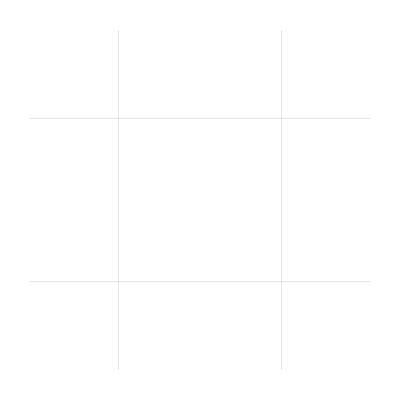

```mathematica
Field=Graphics[{},GridLines->{{-1,0,1,2}, {-1,0,1,2}},PlotRange->{{-0.5,1.5},{-0.5,1.5}}]
```

```mathematica
Graphics//Options
```

```mathematica
ClickPane[Field=Join[]]
```

```mathematica
DynamicModule[{pt={0,0}},ClickPane[Field=Join[Field],},PlotRange->5],(pt=#)&]]
```

```mathematica
DynamicModule[{pt={0,0}},
ClickPane[
Field=Show[Field,Graphics[{Dynamic@Disk[pt,0.1]}]],
(pt=#)&,Method->"Queued"]]
```

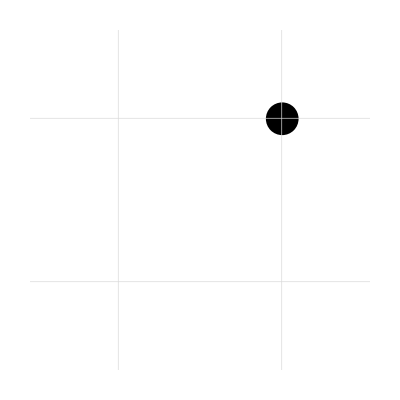

```mathematica
Show[Field,Graphics[{Disk[pt,0.1]}]]
```

```mathematica
ClearAll[pt]
```

```mathematica
pt={1,0}
```

{1,0}

```mathematica
ClickPane//Options
```

{Method→Preemptive,PassEventsDown→Automatic,PassEventsUp→True}

```mathematica
Field
```

-Graphics-

```mathematica
Show[Field,Graphics[{Disk[pt,0.1]}]]
```

-Graphics-

```mathematica
S=Show[Field,Graphics[{Disk[pt,0.1]}]]
```

-Graphics-

```mathematica
DynamicModule[{pts={}},ClickPane[Dynamic[Framed@Graphics[Line[pts],PlotRange->1]],AppendTo[pts,#]&]]
```

```mathematica
DynamicModule[{pts={}},ClickPane[Dynamic[Framed@Graphics[Line[pts],PlotRange->1]],AppendTo[pts,#]&]]
```